# Point Force Greens Function Solutions

```mathematica
r = Sqrt[(x-xs)^2 +(y-ys)^2];
u1f =Integrate[1/2/Pi*Log[r],ys,GeneratedParameters->C];
u1fe = ReplaceAll[u1f,{xs->0,ys->a}] - ReplaceAll[u1f,{xs->0,ys->-a}]//FullSimplify
```

(-4 a+2 x (ArcTan[(a-y)/x]+ArcTan[(a+y)/x])+(a-y) Log[x^2+(a-y)^2]+(a+y) Log[x^2+(a+y)^2])/(4 π)

```mathematica
u1fex0 =Limit[u1fe,x->0]
```

(-4 a+(a-y) Log[(a-y)^2]+(a+y) Log[(a+y)^2])/(4 π)

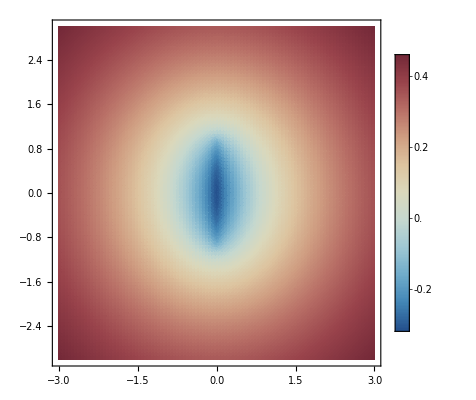

```mathematica
DensityPlot[ReplaceAll[u1fe,{a->1}],{x,-3,3},{y,-3,3},ColorFunction->ColorData[{"RedBlueTones","Reverse"}],PlotLegends->Automatic,PlotRange->All,PlotPoints->100]
```

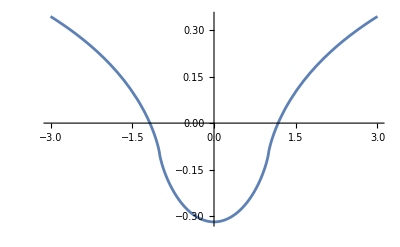

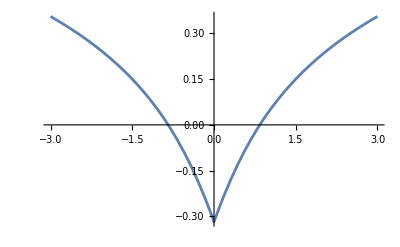

```mathematica
p1=Plot[ReplaceAll[u1fex0,a->1],{y,-3,3}]
p2=Plot[ReplaceAll[u1fe,{a->1,y->0}],{x,-3,3}]
```

## Calculate Stresses

```mathematica
sigma12 =ArcTan[(x^2 + y^2 - a^2),2*a*x]/2/Pi//Simplify
sigma13=D[u1fe,y]//Simplify
```

ArcTan[-a^2+x^2+y^2,2 a x]/(2 π)

(-Log[x^2+(a-y)^2]+Log[x^2+(a+y)^2])/(4 π)

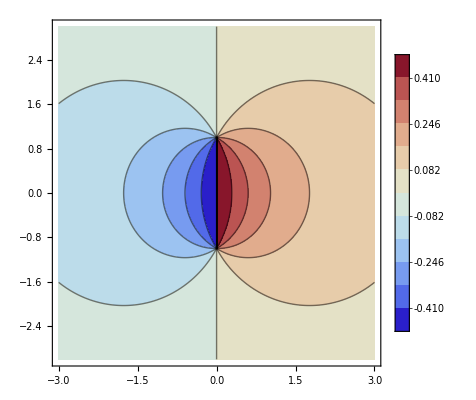

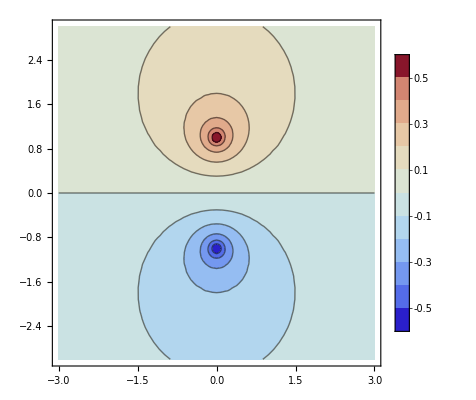

```mathematica
ContourPlot[ReplaceAll[sigma12,a->1],{x,-3,3},{y,-3,3},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->All,PlotPoints->100,Contours->11]
ContourPlot[ReplaceAll[sigma13,a->1],{x,-3,3},{y,-3,3},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->Full,Contours->11]
```

# Slip Greens Function Solution

```mathematica
u1s =Integrate[(x-xs)/((x-xs)^2 +(y-ys)^2),ys,GeneratedParameters->C];
u1se = ReplaceAll[u1s,{xs->0,ys->1}] - ReplaceAll[u1s,{xs->0,ys->-1}]
```

-ArcTan[(-1+y)/x]+ArcTan[(1+y)/x]

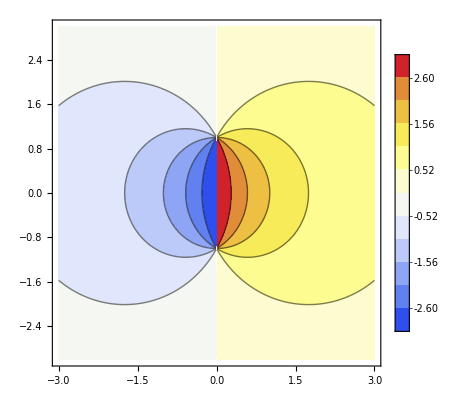

```mathematica
ContourPlot[u1se,{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All,PlotPoints->100,Contours->11]
```